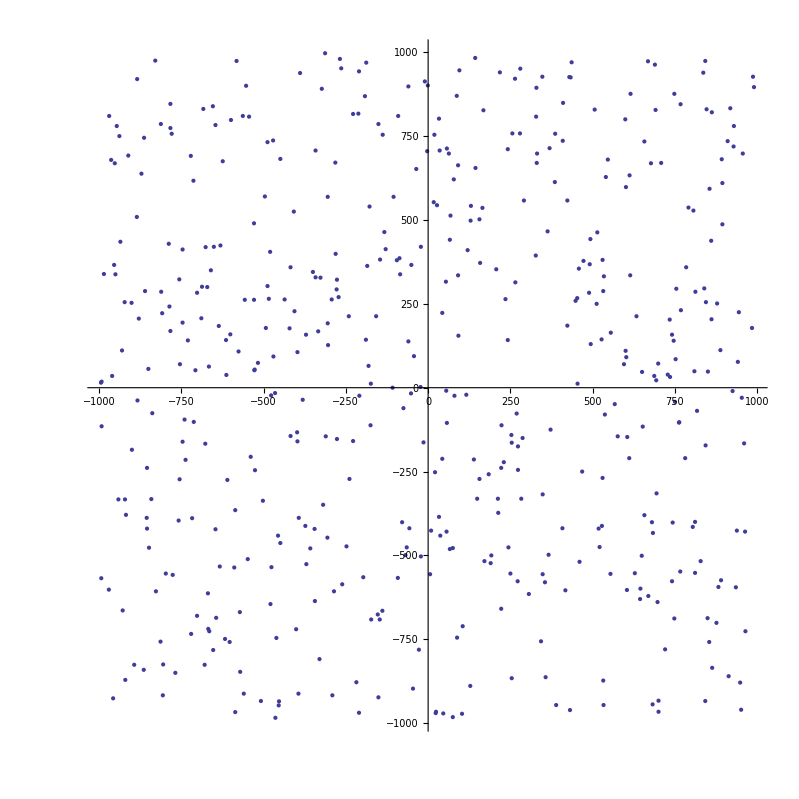

```mathematica
s={290797};
T={};
For[n=1,n<1001,n++,
s=Append[s, Mod[s[[-1]]^2, 50515093]];
T= Append[T,Mod[s[[-1]],2000]-1000];
];
ListPlot[Partition[T,2],AspectRatio->1]
```

```mathematica
PolyArea[pts_]:=Module[{ara}, 
ara = Table[1/2 (pts[[i,1]] pts[[i+1,2]]-pts[[i+1,1]] pts[[i,2]]),{i,1,Length[pts]-1}];
Total[ara] + 1/2 (pts[[Length[pts],1]] pts[[1,2]]-pts[[1,1]] pts[[Length[pts],2]])
]
```

```mathematica
PolyArea[Reverse[{{-1,-1},{-1,1},{1,1},{1,-1}}]]
```

4

```mathematica
pts=Partition[T,2];
tmppts=Select[pts,#[[1]]<0&&#[[1]]>-250&&#[[2]]<0&&#[[2]]>-700&];
ListPlot[tmppts,PlotRange->{{-600,0},{-600,0}},AspectRatio->1]
```